0.0000861733

12

14

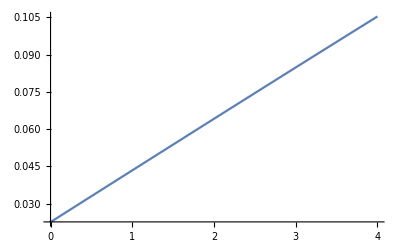

```mathematica
e1[e_,Δ_] := √(e^2-Δ^2);
e2[e_,Δ_,hf_] := √((e+hf)×(e+hf)-Δ×Δ);
e32[e_,Δ_,hf_] := e^2+Δ^2+hf × e;
e4[e_,Δ_] := √(Δ^2-e^2);
g[e_,Δ_,hf_]:=e32[e,Δ,hf]/(e1[e,Δ]×e2[e,Δ,hf]);

g2[e_,Δ_,hf_]:=e32[e,Δ,hf]/(e4[e,Δ]×e2[e,Δ,hf]);

fd[e_,kT_]:=1/(Exp[e/kT]+1);

ff[e_,hf_,kT_]:=fd[e,kT] - fd[e+hf,kT];

f2[e_,hf_,kT_]:=1- 2×fd[e+hf,kT];

int1[e_,Δ_,hf_,kT_]:=ff[e,hf,kT]×g[e,Δ,hf];
int11[e_,Δ_,hf_,kT_]:=f2[e,hf,kT]×g[e,Δ,hf];
int2[e_,Δ_,hf_,kT_]:=f2[e,hf,kT]×g2[e,Δ,hf];

σ1nL[Δ_,hf_,kT_]:=2/hf×NIntegrate[int1[Δ+x^2,Δ,hf,kT]2x,{x,0,20 Δ^(1/2)}];
σ1nU[Δ_,hf_,kT_]:=1/hf(NIntegrate[int11[Δ-hf+x^2,Δ,hf,kT]2x,{x,0,√(hf/2-Δ)}]+NIntegrate[int11[-Δ-x^2,Δ,hf,kT]2x,{x,0,√(hf/2-Δ)}]);
σ1n[Δ_,hf_,kT_]:=
If[hf≤2×Δ,
σ1nL[Δ,hf,kT],
σ1nL[Δ,hf,kT]-σ1nU[Δ,hf,kT]
];

σ2nL[Δ_,hf_,kT_]:=1/hf(NIntegrate[int2[Δ-hf+x^2,Δ,hf,kT]2x,{x,0,√(hf/2)}]+NIntegrate[int2[Δ-x^2,Δ,hf,kT]2x,{x,0,√(hf/2)}]);

σ2nU[Δ_,hf_,kT_]:=1/hf(NIntegrate[int2[-Δ+x^2,Δ,hf,kT]2x,{x,0,√Δ}]+ NIntegrate[int2[Δ-x^2,Δ,hf,kT]2x,{x,0,√Δ}]);

σ2n[Δ_,hf_,kT_]:=
If[hf≤2Δ,
σ2nL[Δ,hf,kT],
σ2nU[Δ,hf,kT]
];


σn[Δ_,hf_,kT_]:=σ1n[Δ,hf,kT]-ⅈ×σ2n[Δ,hf,kT];



kB = 8.617333262×10^-5


Δo[Tc_]:= 1.764×kB×Tc;
cΔ[T_,Tc_]:= Δo[Tc]×√(Cos[π/2(T/Tc)^2]);



T = 12
Tc = 14


Plot[Re[σn[cΔ[T,Tc],x,T]],{x,0,4}]
```